```mathematica
description="Slepton-side photon radiation";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
```

### Get amplitudes

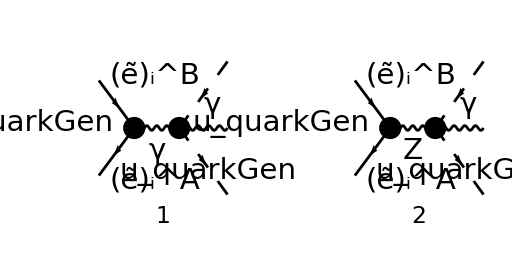

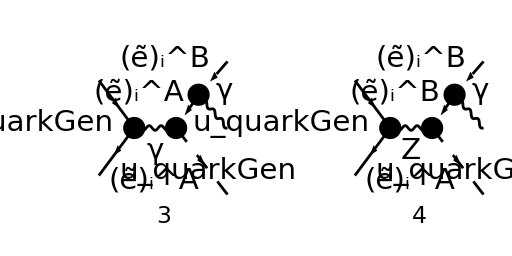

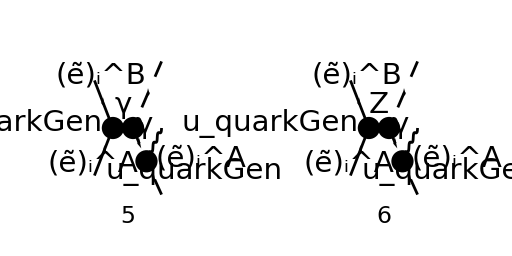

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],F[3]}
(*F[3] to get rid of diagrams with quark-side radiation*)
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
LorentzIndexNames->{μ,ν,ρ},
(*Contract->True,*)
DropSumOver->True,
SMP->True
]/.{MQU[quarkGen]->0}
```

{-(2 ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μρ (ε^*)^μ(k) g^νρ e^2)/(k+k_1+k_2)^2,(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μρ (ε^*)^μ(k) g^νρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2)/((k+k_1+k_2)^2 ((-k-k_1)^2-(MSf(A,2,i))^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((-k-k_1)^2-(MSf(B,2,i))^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2)/((k+k_1+k_2)^2 ((k+k_2)^2-(MSf(A,2,i))^2)),(ⅈ (φ(-p_2)).((2 ⅈ γ^ν.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^ν.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(2 ((k+k_2)^2-(MSf(A,2,i))^2) ((k+k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

Change  to for quark charge in photon diagram.

```mathematica
Mγ[0]=Total[Mlist[0][[{1,3,5}]]] 3/2 SMP["e_Q"]//Simplify
```

-1/(2 (k+k_1+k_2)^2)3 ⅈ e^2 e_Q g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)) (((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(A,2,i))^2)+((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+2 g^μρ)

Change slepton propagator in B-radiation diagram to match that of the Z-diagrams (the slepton masses can be interchanged in the photon diagram because of the Kronecker-delta)

```mathematica
Mγ[1]=Mγ[0]/.{
FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[-k-k1,D],MSf[B,2,i]]]}
```

-1/(2 (k+k_1+k_2)^2)3 ⅈ e^2 e_Q g^νρ (ε^*)^μ(k) IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ)

Substitute for Cγ for easier comparison to my notes. Note that there is an “e” stuck inbetween the spinors, so I replace the expression for Cγ/e.

```mathematica
Mγ[2]=Mγ[1]/.{SMP["e"]^2SMP["e_Q"]IndexDelta[A,B]FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],0]]->Cγ/SMP["e"]}
```

-(3 ⅈ Cγ g^νρ (ε^*)^μ(k) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ))/(2 e)

Simplify Z diagrams by writing them in terms of Zql, Zqr and ZliAB

```mathematica
MZ[0]=Total[Mlist[0][[{2,4,6}]]];
MZ[1]=MZ[0]/.{4 SMP["sin_W"]^2-3:>12 Zql};
MZ[2]=MZ[1]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])};
MZ[3]=MZ[2]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify;
MZ[4]=MZ[3]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

-((ⅈ e^2 ZliAB g^νρ (ε^*)^μ(k) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1)))/((cos(θ_W)) (sin(θ_W)) ((k+k_1+k_2)^2-m_Z^2)))

Substitute for CZ for easier comparison to my notes.

```mathematica
MZ[5]=MZ[4]/.{SMP["e"]^2 ZliAB FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1+k2,D],SMP["m_Z"]]]->CZ SMP["sin_W"]^2SMP["cos_W"]^2/SMP["e"]}
```

-1/e ⅈ CZ (cos(θ_W)) g^νρ (ε^*)^μ(k) (sin(θ_W)) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))

```mathematica
M[0]=Mγ[2]+MZ[5]
```

-1/e ⅈ CZ (cos(θ_W)) g^νρ (ε^*)^μ(k) (sin(θ_W)) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))-(3 ⅈ Cγ g^νρ (ε^*)^μ(k) (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)) (((-k-2 k_2)^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ))/(2 e)

```mathematica
(*M[1]=M[0]/.{Pair[Momentum[k,D],Momentum[Polarization[k,-I],D]]->0}*)
```

```mathematica
M[1]=M[0]//ExpandScalarProduct//Simplify
```

-1/(2 e)ⅈ g^νρ (ε^*)^μ(k) (-((k^μ+2 k_2^μ) (k^ρ-k_1^ρ+k_2^ρ))/((k+k_2)^2-(MSf(A,2,i))^2)-((k^μ+2 k_1^μ) (k^ρ+k_1^ρ-k_2^ρ))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (2 CZ (cos(θ_W)) (sin(θ_W)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))+3 Cγ (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)))

Simplify by getting rid of ’s: Note first that M is proportional to

```mathematica
M[1]//Collect2[#,Momentum[Polarization[k,-I],D],IsolateNames->KK]&
```

-1/2 ⅈ KK(156) (ε^*)^μ(k)

Thus, since , we can set all .

```mathematica
M[2]=M[1]/.{Pair[LorentzIndex[μ,D],Momentum[k,D]]->0}
```

-1/(2 e)ⅈ g^νρ (ε^*)^μ(k) (-(2 k_2^μ (k^ρ-k_1^ρ+k_2^ρ))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 k_1^μ (k^ρ+k_1^ρ-k_2^ρ))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (2 CZ (cos(θ_W)) (sin(θ_W)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))+3 Cγ (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)))

```mathematica
M[3]=M[2]//MomentumCombine
```

-1/(2 e)ⅈ g^νρ (ε^*)^μ(k) (-(2 k_2^μ (k-k_1+k_2)^ρ)/((k+k_2)^2-(MSf(A,2,i))^2)-(2 k_1^μ (k+k_1-k_2)^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (2 CZ (cos(θ_W)) (sin(θ_W)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))+3 Cγ (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)))

Impose momentum conservation  for further simplification using the Dirac equation.

```mathematica
M[4]=M[3]/.{
Momentum[k+k2-k1,D]->Momentum[p1+p2-2k1,D],
Momentum[k+k1-k2,D]->Momentum[p1+p2-2k2,D]
}//ExpandScalarProduct
```

-1/(2 e)ⅈ g^νρ (ε^*)^μ(k) (-(2 k_2^μ (-2 k_1^ρ+p_1^ρ+p_2^ρ))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 k_1^μ (-2 k_2^ρ+p_1^ρ+p_2^ρ))/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (2 CZ (cos(θ_W)) (sin(θ_W)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))+3 Cγ (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)))

Note that the Dirac expression is  (or the same, but no chiral projection) for all terms, and since the expression has a factor , any   or  disappear by the Dirac equation. We can use this to get a form that is easier to compare with my hand calculations:

```mathematica
Mtest[0]=M[4]/.{
Pair[LorentzIndex[ρ,D],Momentum[p1,D]]->0,
Pair[LorentzIndex[ρ,D],Momentum[p2,D]]->0
}
```

-1/(2 e)ⅈ g^νρ (ε^*)^μ(k) ((4 k_1^ρ k_2^μ)/((k+k_2)^2-(MSf(A,2,i))^2)+(4 k_1^μ k_2^ρ)/((-k-k_1)^2-(MSf(B,2,i))^2)+2 g^μρ) (2 CZ (cos(θ_W)) (sin(θ_W)) (φ(-p_2)).(2 ⅈ e δ_Col1Col2 (Zql γ^ν.(γ̄)^7+Zqr γ^ν.(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(p_1))+3 Cγ (φ(-p_2)).(-2/3 ⅈ e γ^ν δ_Col1Col2).(φ(p_1)))

```mathematica
Mtest[1]=Mtest[0]//Contract//DiracSimplify
```

(8 CZ Zql δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 CZ Zqr δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 CZ Zql δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+(8 CZ Zqr δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+4 CZ Zql δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+4 CZ Zqr δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))-(4 Cγ δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(4 Cγ δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-2 Cγ δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))

```mathematica
M[5]=M[4]//DiracSimplify
```

(8 CZ Zql δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 CZ Zqr δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 CZ Zql δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+(8 CZ Zqr δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+4 CZ Zql δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+4 CZ Zqr δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1))-(4 Cγ δ_Col1Col2 (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(4 Cγ δ_Col1Col2 (k_1·ε^*(k)) (φ(-p_2)).(γ·k_2).(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-2 Cγ δ_Col1Col2 (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))

```mathematica
Mothertest[0]=M[3]//DiracSimplify
```

-2 Cγ (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) δ_Col1Col2+4 CZ Zqr (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) δ_Col1Col2+4 CZ Zql (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) δ_Col1Col2+(2 Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)+(2 Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)-(2 Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)+(4 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)+(4 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) δ_Col1Col2)/((k+k_1)^2-(MSf(B,2,i))^2)+(2 Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)-(2 Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)+(2 Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)-(4 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)-(4 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)+(4 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)+(4 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)-(4 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)-(4 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_2·ε^*(k)) δ_Col1Col2)/((k+k_2)^2-(MSf(A,2,i))^2)

```mathematica
FCCompareResults[{Mtest[1]},{M[5]}];
```

Check of the results: The results agree.

```mathematica
M[6]=M[5]//Uncontract[#,Polarization[k,-I],Pair->All]&
```

(8 CZ Zql δ_Col1Col2 k_2^($AL($546)) (ε^*)^($AL($546))(k) (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(8 CZ Zqr δ_Col1Col2 k_2^($AL($545)) (ε^*)^($AL($545))(k) (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)+(4 CZ Zql δ_Col1Col2 k_1^($AL($543)) (ε^*)^($AL($543))(k) (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+(4 CZ Zqr δ_Col1Col2 k_1^($AL($542)) (ε^*)^($AL($542))(k) (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zql δ_Col1Col2 k_1^($AL($541)) (ε^*)^($AL($541))(k) (φ(-p_2)).(γ·(k+k_1)).(γ̄)^7.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-(4 CZ Zqr δ_Col1Col2 k_1^($AL($540)) (ε^*)^($AL($540))(k) (φ(-p_2)).(γ·(k+k_1)).(γ̄)^6.(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+4 CZ Zql δ_Col1Col2 (ε^*)^($AL($558))(k) (φ(-p_2)).γ^($AL($558)).(γ̄)^7.(φ(p_1))+4 CZ Zqr δ_Col1Col2 (ε^*)^($AL($557))(k) (φ(-p_2)).γ^($AL($557)).(γ̄)^6.(φ(p_1))-(4 Cγ δ_Col1Col2 k_2^($AL($544)) (ε^*)^($AL($544))(k) (φ(-p_2)).(γ·k_1).(φ(p_1)))/((k+k_2)^2-(MSf(A,2,i))^2)-(2 Cγ δ_Col1Col2 k_1^($AL($539)) (ε^*)^($AL($539))(k) (φ(-p_2)).(γ·k_2).(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)+(2 Cγ δ_Col1Col2 k_1^($AL($538)) (ε^*)^($AL($538))(k) (φ(-p_2)).(γ·(k+k_1)).(φ(p_1)))/((k+k_1)^2-(MSf(B,2,i))^2)-2 Cγ δ_Col1Col2 (ε^*)^($AL($556))(k) (φ(-p_2)).γ^($AL($556)).(φ(p_1))

### Simplify amplitudes

```mathematica
FCClearScalarProducts[];
(*SetMandelstam[x,{p1,p2,-k1,-k,-k2},{0,0,MSf[B,2,i],0,MSf[A,2,i]}];*)
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M[2]=M[1]//FeynAmpDenominatorExplicit//DiracSimplify//Simplify
```

-1/(2 (k·k_1) (k·k_2))(4 Cγ (φ(-p_2)).(γ·ε^*(k)).(φ(p_1)) (k·k_1) (k·k_2)-8 CZ Zqr (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)) (k·k_1) (k·k_2)-8 CZ Zql (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1)) (k·k_1) (k·k_2)-Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k·ε^*(k)) (k·k_2)-Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k·ε^*(k)) (k·k_2)+Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k·ε^*(k)) (k·k_2)+2 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k·ε^*(k)) (k·k_2)+2 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k·ε^*(k)) (k·k_2)+2 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·ε^*(k)) (k·k_2)+2 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·ε^*(k)) (k·k_2)-2 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·ε^*(k)) (k·k_2)-2 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·ε^*(k)) (k·k_2)-2 Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k_1·ε^*(k)) (k·k_2)-2 Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1·ε^*(k)) (k·k_2)+2 Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k_1·ε^*(k)) (k·k_2)+4 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)+4 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)+4 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)+4 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)-4 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)-4 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k_1·ε^*(k)) (k·k_2)-Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k·k_1) (k·ε^*(k))+Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k·k_1) (k·ε^*(k))-Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k·k_1) (k·ε^*(k))+2 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k·k_1) (k·ε^*(k))+2 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k·k_1) (k·ε^*(k))-2 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·k_1) (k·ε^*(k))-2 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·k_1) (k·ε^*(k))+2 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·k_1) (k·ε^*(k))+2 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·k_1) (k·ε^*(k))-2 Cγ (φ(-p_2)).(γ·k).(φ(p_1)) (k·k_1) (k_2·ε^*(k))+2 Cγ (φ(-p_2)).(γ·k_1).(φ(p_1)) (k·k_1) (k_2·ε^*(k))-2 Cγ (φ(-p_2)).(γ·k_2).(φ(p_1)) (k·k_1) (k_2·ε^*(k))+4 CZ Zqr (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)) (k·k_1) (k_2·ε^*(k))+4 CZ Zql (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1)) (k·k_1) (k_2·ε^*(k))-4 CZ Zqr (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)) (k·k_1) (k_2·ε^*(k))-4 CZ Zql (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)) (k·k_1) (k_2·ε^*(k))+4 CZ Zqr (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)) (k·k_1) (k_2·ε^*(k))+4 CZ Zql (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)) (k·k_1) (k_2·ε^*(k))) δ_Col1Col2

### Square amplitude

```mathematica
MCC[0]=ComplexConjugate[M[2]]
```

```mathematica
Msquared[0]=M[2]MCC[0]
```

```mathematica
Msquared[1]=Msquared[0]//DiracSimplify//Simplify
```

```mathematica
Msquared[2]=Msquared[1]//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//SUNSimplify[#,SUNNToCACF->False]&//DiracSimplify//Simplify
```